# Quantum Circuit Implementing Grover's Algorithm

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx

## Introduction

This is a tutorial on the use of Quantum`Computing` Mathematica add-on to implement Grover's Algorithm using Quantum Gates.
Grover's algorithm is a quantum algorithm for searching an unsorted database with N entries in O(N^(1/2)) time and using O(log N) storage space (Grover L.K.: A fast quantum mechanical algorithm for database search, Proceedings, 28th Annual ACM Symposium on the Theory of Computing, (May 1996) p. 212).
Grover's algorithm can be generalized to "Quantum Counting" (Brassard G., P. Hoyer and Al. Tapp, arXiv:quant-ph/9805082) and "Quantum Amplitude Amplification and Estimation" (Brassard G., P. Hoyer, M. Mosca and A. Tapp, arXiv:quant-ph/0005055).
A Mathematica "Demonstration" implementing Grover's Algorithm can be found in this link:
Alexander Prokopenya, "Quantum Circuit Implementing Grover's Search Algorithm" from The Wolfram Demonstrations Project
http://demonstrations.wolfram.com/QuantumCircuitImplementingGroversSearchAlgorithm/

## Load the Package

First load the Quantum`Computing` package. Write:
Needs["Quantum`Computing`"];
then press at the same time the keys ⇧-⌤ to evaluate. Mathematica will load the package:

```mathematica
Needs["Quantum`Computing`"]
```

Quantum`Computing` Version 2.2.0. (July 2010) 
A Mathematica package for Quantum Computing in Dirac bra-ket notation and plotting of quantum circuits
by José Luis Gómez-Muñoz

Execute SetComputingAliases[] in order to use the keyboard to enter quantum objects in Dirac's notation
SetComputingAliases[] must be executed again in each new notebook that is created

In order to use the keyboard to enter quantum objects write:
SetComputingAliases[ ];
then press at the same time the keys ⇧-⌤ to evaluate. The semicolon prevents Mathematica from printing the help message. Remember that SetComputingAliases[ ] must be evaluated again in each new notebook:

```mathematica
SetComputingAliases[];
```

## Circuit implementation of Gover's Algorithm for two qubits

Following commands show and calculate the quantum circuit implementation of Grover's Algorithm for selecting the ket that represents the number k=1 as a two-qbit binary number (0_1 | 1_2). Please continue reading below for a detailed explanation.

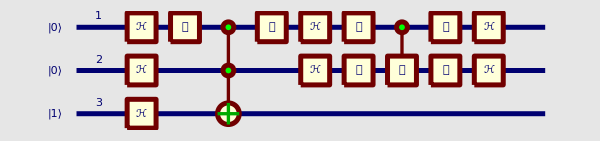
ℋ_{OverHat[1],OverHat[2]}·𝒳_{OverHat[1],OverHat[2]}·𝒞^{OverHat[1]}[𝒵_OverHat[2]]·𝒳_{OverHat[1],OverHat[2]}·ℋ_{OverHat[1],OverHat[2]}·𝒳_{OverHat[1]}·𝒞^{OverHat[1],OverHat[2]}[𝒩𝒪𝒯_OverHat[3]]·𝒳_{OverHat[1]}·ℋ_{OverHat[1],OverHat[2],OverHat[3]}·|0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩
-Graphics-
Probability | Measurement | State
1. | (0_1 | 1_2) | 0.707107 (|011⟩-1. |010⟩)
Probability | Measurement | State

```mathematica
n=2;
k=1;
it=1;
mylist=Flatten[Position[IntegerDigits[k,2,n],0]];
circuit=(Subscript[ℋ, n]·Subscript[𝒳, n]·(𝒞^(n-1))[Subscript[𝒵, n̂]]·Subscript[𝒳, n]·Subscript[ℋ, n]·Subscript[𝒳, mylist]·(𝒞^n)[Subscript[𝒩𝒪𝒯, OverHat[n+1]]]·Subscript[𝒳, mylist])^it·Subscript[ℋ, n+1]·(|Subscript[0, OverHat[1]]⟩)^(⊗n)·|Subscript[1, OverHat[n+1]]⟩;
Column[{
circuit,
QuantumPlot[
circuit,ImageSize->{600,Automatic}],
TraditionalForm[N[QuantumEvaluate[QubitMeasurement[circuit,n,FactorKet->False]]]]
  }]
```

Following commands show and calculate the quantum circuit implementation of Grover's Algorithm for selecting the ket that represents the number k=2 as a binary number (1_1 | 0_2). See the difference with the previous circuit. The working of this circuit is explained below in this document.

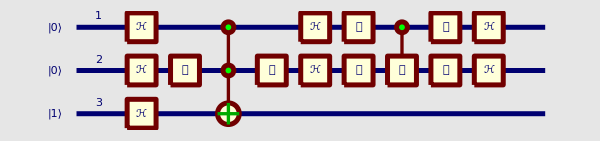
ℋ_{OverHat[1],OverHat[2]}·𝒳_{OverHat[1],OverHat[2]}·𝒞^{OverHat[1]}[𝒵_OverHat[2]]·𝒳_{OverHat[1],OverHat[2]}·ℋ_{OverHat[1],OverHat[2]}·𝒳_{OverHat[2]}·𝒞^{OverHat[1],OverHat[2]}[𝒩𝒪𝒯_OverHat[3]]·𝒳_{OverHat[2]}·ℋ_{OverHat[1],OverHat[2],OverHat[3]}·|0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩
-Graphics-
Probability | Measurement | State
1. | (1_1 | 0_2) | 0.707107 (|101⟩-1. |100⟩)
Probability | Measurement | State

```mathematica
n=2;
k=2;
it=1;
mylist=Flatten[Position[IntegerDigits[k,2,n],0]];
circuit=(Subscript[ℋ, n]·Subscript[𝒳, n]·(𝒞^(n-1))[Subscript[𝒵, n̂]]·Subscript[𝒳, n]·Subscript[ℋ, n]·Subscript[𝒳, mylist]·(𝒞^n)[Subscript[𝒩𝒪𝒯, OverHat[n+1]]]·Subscript[𝒳, mylist])^it·Subscript[ℋ, n+1]·(|Subscript[0, OverHat[1]]⟩)^(⊗n)·|Subscript[1, OverHat[n+1]]⟩;
Column[{
circuit,
QuantumPlot[
circuit,ImageSize->{600,Automatic}],
TraditionalForm[N[QuantumEvaluate[QubitMeasurement[circuit,n,FactorKet->False]]]]
  }]
```

## Step-by-step explanation of the circuit implementing Grover's Algorithm for two qubits

### Initial State

An equally weighted superposition of all basis-states is generated using three Hadamard gates.
Notice that at this stage all the kets having a positive sign have the ancillary qubit set to 0_OverHat[3] , and all the kets having a negative sign have the ancillary qubit set to 1_OverHat[3]
The state of the system is stored in |g1⟩

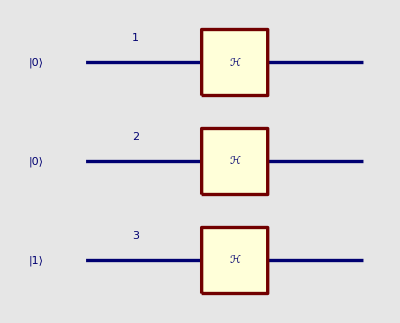
ℋ_{OverHat[1],OverHat[2],OverHat[3]}·|0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩
-Graphics-
(|0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)

```mathematica
n=2;
circuitpart=Subscript[ℋ, n+1]·(|Subscript[0, OverHat[1]]⟩)^(⊗n)·|Subscript[1, OverHat[n+1]]⟩;
Column[{
circuitpart,
QuantumPlot[circuitpart],
|g1⟩=QuantumEvaluate[circuitpart]}]
```

### Changing the phase of those kets that meet the search criteria

The search criteria in this example is to represent the number 2 in binary digits: (1_OverHat[1],0_OverHat[2]), those kets that meet the criteria get their phase changed (the signs plus and minus are exchanged). The conditional negation of the ancillary qubit gives this change of sign.
The state of the system is stored in |g2⟩

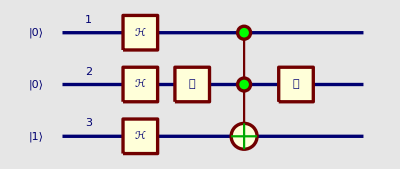
𝒳_{OverHat[2]}·𝒞^{OverHat[1],OverHat[2]}[𝒩𝒪𝒯_OverHat[3]]·𝒳_{OverHat[2]}·ℋ_{OverHat[1],OverHat[2],OverHat[3]}·|0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩
-Graphics-
(|0_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|0_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|0_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(2 √2)+(|1_OverHat[1],1_OverHat[2],0_OverHat[3]⟩)/(2 √2)-(|1_OverHat[1],1_OverHat[2],1_OverHat[3]⟩)/(2 √2)

```mathematica
n=2;
k=2;
mylist=Flatten[Position[IntegerDigits[k,2,n],0]];
circuitpart=Subscript[𝒳, mylist]·(𝒞^n)[Subscript[𝒩𝒪𝒯, OverHat[n+1]]]·Subscript[𝒳, mylist]·Subscript[ℋ, n+1]·(|Subscript[0, OverHat[1]]⟩)^(⊗n)·|Subscript[1, OverHat[n+1]]⟩;
Column[{
circuitpart,
QuantumPlot[circuitpart],
|g2⟩=QuantumEvaluate[circuitpart]}]
```

It is very important to understand the difference between the states just after the Hadamard gates (|g1⟩), and the state after the conditional change of sign (phase) for those kets that meet the criteria (|g2⟩):

```mathematica
TraditionalForm[Column[{"The sign was changed (+↔-) only on those kets that meet the search criteria",|g1⟩,|g2⟩},Dividers->All]]
```

The sign was changed (+↔-) only on those kets that meet the search criteria
(|000⟩)/(2 √2)-(|001⟩)/(2 √2)+(|010⟩)/(2 √2)-(|011⟩)/(2 √2)+(|100⟩)/(2 √2)-(|101⟩)/(2 √2)+(|110⟩)/(2 √2)-(|111⟩)/(2 √2)
(|000⟩)/(2 √2)-(|001⟩)/(2 √2)+(|010⟩)/(2 √2)-(|011⟩)/(2 √2)-(|100⟩)/(2 √2)+(|101⟩)/(2 √2)+(|110⟩)/(2 √2)-(|111⟩)/(2 √2)

### Increasing the amplitude of those kets that had their phase changed

The rest of the circuit increases the amplitude of those kets that had their phase changed.
In the case of two qubits, the other kets get their amplitude reduced to zero.

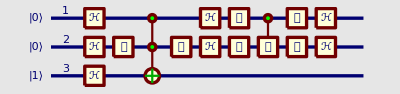
ℋ_{OverHat[1],OverHat[2]}·𝒳_{OverHat[1],OverHat[2]}·𝒞^{OverHat[1]}[𝒵_OverHat[2]]·𝒳_{OverHat[1],OverHat[2]}·ℋ_{OverHat[1],OverHat[2]}·𝒳_{OverHat[2]}·𝒞^{OverHat[1],OverHat[2]}[𝒩𝒪𝒯_OverHat[3]]·𝒳_{OverHat[2]}·ℋ_{OverHat[1],OverHat[2],OverHat[3]}·|0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩
-Graphics-
-(|1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩)/(√2)+(|1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(√2)

```mathematica
n=2;
k=2;
mylist=Flatten[Position[IntegerDigits[k,2,n],0]];
circuitpart=Subscript[ℋ, n]·Subscript[𝒳, n]·(𝒞^(n-1))[Subscript[𝒵, n̂]]·Subscript[𝒳, n]·Subscript[ℋ, n]·Subscript[𝒳, mylist]·(𝒞^n)[Subscript[𝒩𝒪𝒯, OverHat[n+1]]]·Subscript[𝒳, mylist]·Subscript[ℋ, n+1]·(|Subscript[0, OverHat[1]]⟩)^(⊗n)·|Subscript[1, OverHat[n+1]]⟩;
Column[{
circuitpart,
QuantumPlot[circuitpart],
QuantumEvaluate[circuitpart]}]
```

### Measurement gives with those kets that had their amplitude increased

In the case of two qubits, measurment will give those values that satisfy the search criteria with a 100% of probability

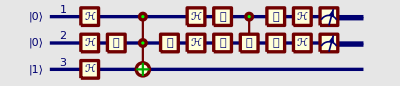
QubitMeasurement[ℋ_{OverHat[1],OverHat[2]}·𝒳_{OverHat[1],OverHat[2]}·𝒞^{OverHat[1]}[𝒵_OverHat[2]]·𝒳_{OverHat[1],OverHat[2]}·ℋ_{OverHat[1],OverHat[2]}·𝒳_{OverHat[2]}·𝒞^{OverHat[1],OverHat[2]}[𝒩𝒪𝒯_OverHat[3]]·𝒳_{OverHat[2]}·ℋ_{OverHat[1],OverHat[2],OverHat[3]}·|0_OverHat[1],0_OverHat[2],1_OverHat[3]⟩,{OverHat[1],OverHat[2]},FactorKet→False]
-Graphics-
Probability | Measurement | State
1 | {{1_OverHat[1],0_OverHat[2]}} | (-|1_OverHat[1],0_OverHat[2],0_OverHat[3]⟩+|1_OverHat[1],0_OverHat[2],1_OverHat[3]⟩)/(√2)
Probability | Measurement | State

```mathematica
n=2;
k=2;
mylist=Flatten[Position[IntegerDigits[k,2,n],0]];
circuitpart=QubitMeasurement[Subscript[ℋ, n]·Subscript[𝒳, n]·(𝒞^(n-1))[Subscript[𝒵, n̂]]·Subscript[𝒳, n]·Subscript[ℋ, n]·Subscript[𝒳, mylist]·(𝒞^n)[Subscript[𝒩𝒪𝒯, OverHat[n+1]]]·Subscript[𝒳, mylist]·Subscript[ℋ, n+1]·(|Subscript[0, OverHat[1]]⟩)^(⊗n)·|Subscript[1, OverHat[n+1]]⟩,n,FactorKet->False];
Column[{
circuitpart,
QuantumPlot[circuitpart],
QuantumEvaluate[circuitpart]}]
```

## Circuit implementation of Gover's Algorithm for three qubits

Following commands show and calculate the quantum circuit implementation of Grover's Algorithm for selecting the ket that represents the number k=6 as a three-qubit binary number (1_1 | 1_2 | 0_3). Please continue reading below for a detailed explanation. The use of the standard Mathematica command Expand[] makes the calculation faster because it expands the power of the operators:

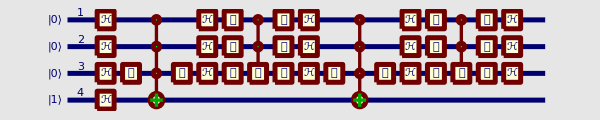
ℋ_{OverHat[1],OverHat[2],OverHat[3]}·𝒳_{OverHat[1],OverHat[2],OverHat[3]}·𝒞^{OverHat[1],OverHat[2]}[𝒵_OverHat[3]]·𝒳_{OverHat[1],OverHat[2],OverHat[3]}·ℋ_{OverHat[1],OverHat[2],OverHat[3]}·𝒳_{OverHat[3]}·𝒞^{OverHat[1],OverHat[2],OverHat[3]}[𝒩𝒪𝒯_OverHat[4]]·𝒳_{OverHat[3]}·ℋ_{OverHat[1],OverHat[2],OverHat[3]}·𝒳_{OverHat[1],OverHat[2],OverHat[3]}·𝒞^{OverHat[1],OverHat[2]}[𝒵_OverHat[3]]·𝒳_{OverHat[1],OverHat[2],OverHat[3]}·ℋ_{OverHat[1],OverHat[2],OverHat[3]}·𝒳_{OverHat[3]}·𝒞^{OverHat[1],OverHat[2],OverHat[3]}[𝒩𝒪𝒯_OverHat[4]]·𝒳_{OverHat[3]}·ℋ_{OverHat[1],OverHat[2],OverHat[3],OverHat[4]}·|0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩
-Graphics-
Probability | Measurement | State
0.0078125 | (0_1 | 0_2 | 0_3) | 0.707107 (|0001⟩-1. |0000⟩)
0.0078125 | (0_1 | 0_2 | 1_3) | 0.707107 (|0011⟩-1. |0010⟩)
0.0078125 | (0_1 | 1_2 | 0_3) | 0.707107 (|0101⟩-1. |0100⟩)
0.0078125 | (0_1 | 1_2 | 1_3) | 0.707107 (|0111⟩-1. |0110⟩)
0.0078125 | (1_1 | 0_2 | 0_3) | 0.707107 (|1001⟩-1. |1000⟩)
0.0078125 | (1_1 | 0_2 | 1_3) | 0.707107 (|1011⟩-1. |1010⟩)
0.945313 | (1_1 | 1_2 | 0_3) | 0.707107 (|1100⟩-1. |1101⟩)
0.0078125 | (1_1 | 1_2 | 1_3) | 0.707107 (|1111⟩-1. |1110⟩)
Probability | Measurement | State

```mathematica
n=3;
k=6;
it=2;
mylist=Flatten[Position[IntegerDigits[k,2,n],0]];
circuit=Expand[(Subscript[ℋ, n]·Subscript[𝒳, n]·(𝒞^(n-1))[Subscript[𝒵, n̂]]·Subscript[𝒳, n]·Subscript[ℋ, n]·Subscript[𝒳, mylist]·(𝒞^n)[Subscript[𝒩𝒪𝒯, OverHat[n+1]]]·Subscript[𝒳, mylist])^it·Subscript[ℋ, n+1]·(|Subscript[0, OverHat[1]]⟩)^(⊗n)·|Subscript[1, OverHat[n+1]]⟩];
Column[{
circuit,
QuantumPlot[
circuit,ImageSize->{600,Automatic}],
TraditionalForm[N[QuantumEvaluate[QubitMeasurement[circuit,n,FactorKet->False]]]]
  }]
```

Following commands show and calculate the quantum circuit implementation of Grover's Algorithm for selecting the ket that represents the number k=2 as a three-qubit binary number (0_1 | 1_2 | 0_3). Compare it with the previous circuit. This circuit is explained below in this document. The use of the standard Mathematica command Expand[] makes the calculation faster because it expands the power of the operators:

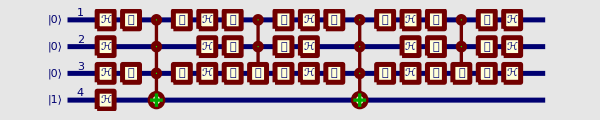
ℋ_{OverHat[1],OverHat[2],OverHat[3]}·𝒳_{OverHat[1],OverHat[2],OverHat[3]}·𝒞^{OverHat[1],OverHat[2]}[𝒵_OverHat[3]]·𝒳_{OverHat[1],OverHat[2],OverHat[3]}·ℋ_{OverHat[1],OverHat[2],OverHat[3]}·𝒳_{OverHat[1],OverHat[3]}·𝒞^{OverHat[1],OverHat[2],OverHat[3]}[𝒩𝒪𝒯_OverHat[4]]·𝒳_{OverHat[1],OverHat[3]}·ℋ_{OverHat[1],OverHat[2],OverHat[3]}·𝒳_{OverHat[1],OverHat[2],OverHat[3]}·𝒞^{OverHat[1],OverHat[2]}[𝒵_OverHat[3]]·𝒳_{OverHat[1],OverHat[2],OverHat[3]}·ℋ_{OverHat[1],OverHat[2],OverHat[3]}·𝒳_{OverHat[1],OverHat[3]}·𝒞^{OverHat[1],OverHat[2],OverHat[3]}[𝒩𝒪𝒯_OverHat[4]]·𝒳_{OverHat[1],OverHat[3]}·ℋ_{OverHat[1],OverHat[2],OverHat[3],OverHat[4]}·|0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩
-Graphics-
Probability | Measurement | State
0.0078125 | (0_1 | 0_2 | 0_3) | 0.707107 (|0001⟩-1. |0000⟩)
0.0078125 | (0_1 | 0_2 | 1_3) | 0.707107 (|0011⟩-1. |0010⟩)
0.945313 | (0_1 | 1_2 | 0_3) | 0.707107 (|0100⟩-1. |0101⟩)
0.0078125 | (0_1 | 1_2 | 1_3) | 0.707107 (|0111⟩-1. |0110⟩)
0.0078125 | (1_1 | 0_2 | 0_3) | 0.707107 (|1001⟩-1. |1000⟩)
0.0078125 | (1_1 | 0_2 | 1_3) | 0.707107 (|1011⟩-1. |1010⟩)
0.0078125 | (1_1 | 1_2 | 0_3) | 0.707107 (|1101⟩-1. |1100⟩)
0.0078125 | (1_1 | 1_2 | 1_3) | 0.707107 (|1111⟩-1. |1110⟩)
Probability | Measurement | State

```mathematica
n=3;
k=2;
it=2;
mylist=Flatten[Position[IntegerDigits[k,2,n],0]];
circuit=Expand[(Subscript[ℋ, n]·Subscript[𝒳, n]·(𝒞^(n-1))[Subscript[𝒵, n̂]]·Subscript[𝒳, n]·Subscript[ℋ, n]·Subscript[𝒳, mylist]·(𝒞^n)[Subscript[𝒩𝒪𝒯, OverHat[n+1]]]·Subscript[𝒳, mylist])^it·Subscript[ℋ, n+1]·(|Subscript[0, OverHat[1]]⟩)^(⊗n)·|Subscript[1, OverHat[n+1]]⟩];
Column[{
circuit,
QuantumPlot[
circuit,ImageSize->{600,Automatic}],
TraditionalForm[N[QuantumEvaluate[QubitMeasurement[circuit,n,FactorKet->False]]]]
  }]
```

## Step-by-step explanation of the circuit implementing Grover's Algorithm for three qubits

### Initial State

An equally weighted superposition of all basis-states is generated using four Hadamard gates.
Notice that at this stage all the kets having a positive sign have the ancillary qubit set to 0_OverHat[4] , and all the kets having a negative sign have the ancillary qubit set to 1_OverHat[4]
The state of the system is stored in |h1⟩

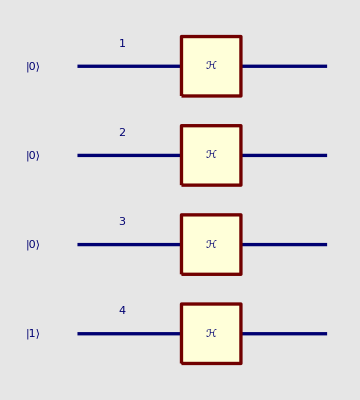
ℋ_{OverHat[1],OverHat[2],OverHat[3],OverHat[4]}·|0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩
-Graphics-
1/4 |0_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-1/4 |0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+1/4 |0_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-1/4 |0_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+1/4 |0_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-1/4 |0_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+1/4 |0_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-1/4 |0_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+1/4 |1_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-1/4 |1_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+1/4 |1_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-1/4 |1_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+1/4 |1_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-1/4 |1_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+1/4 |1_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-1/4 |1_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩

```mathematica
n=3;
circuitpart=Subscript[ℋ, n+1]·(|Subscript[0, OverHat[1]]⟩)^(⊗n)·|Subscript[1, OverHat[n+1]]⟩;
Column[{
circuitpart,
QuantumPlot[circuitpart],
|h1⟩=QuantumEvaluate[circuitpart]}]
```

### Changing the phase of those kets that meet the search criteria

The search criteria in this example is to represent the number 2 in three binary digits: (0_1 | 1_2 | 0_3), those kets that meet the criteria get their phase changed (the signs plus and minus are exchanged). The conditional negation of the ancillary qubit gives this change of sign.
The state of the system is stored in |h2⟩

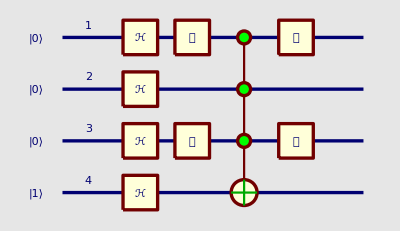
𝒳_{OverHat[1],OverHat[3]}·𝒞^{OverHat[1],OverHat[2],OverHat[3]}[𝒩𝒪𝒯_OverHat[4]]·𝒳_{OverHat[1],OverHat[3]}·ℋ_{OverHat[1],OverHat[2],OverHat[3],OverHat[4]}·|0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩
-Graphics-
1/4 |0_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-1/4 |0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+1/4 |0_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-1/4 |0_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩-1/4 |0_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+1/4 |0_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+1/4 |0_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-1/4 |0_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+1/4 |1_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-1/4 |1_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+1/4 |1_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-1/4 |1_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+1/4 |1_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-1/4 |1_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩+1/4 |1_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩-1/4 |1_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩

```mathematica
n=3;
k=2;
mylist=Flatten[Position[IntegerDigits[k,2,n],0]];
circuitpart=Subscript[𝒳, mylist]·(𝒞^n)[Subscript[𝒩𝒪𝒯, OverHat[n+1]]]·Subscript[𝒳, mylist]·Subscript[ℋ, n+1]·(|Subscript[0, OverHat[1]]⟩)^(⊗n)·|Subscript[1, OverHat[n+1]]⟩;
Column[{
circuitpart,
QuantumPlot[circuitpart],
|h2⟩=QuantumEvaluate[circuitpart]}]
```

It is very important to understand the difference between the states just after the Hadamard gates (|h1⟩), and the state after the conditional change of sign (phase) for those kets that meet the criteria (|h2⟩):

```mathematica
TraditionalForm[Column[{"The sign was changed (+↔-) only on those kets that meet the search criteria",|h1⟩,|h2⟩},Dividers->All]]
```

The sign was changed (+↔-) only on those kets that meet the search criteria
1/4 |0000⟩-1/4 |0001⟩+1/4 |0010⟩-1/4 |0011⟩+1/4 |0100⟩-1/4 |0101⟩+1/4 |0110⟩-1/4 |0111⟩+1/4 |1000⟩-1/4 |1001⟩+1/4 |1010⟩-1/4 |1011⟩+1/4 |1100⟩-1/4 |1101⟩+1/4 |1110⟩-1/4 |1111⟩
1/4 |0000⟩-1/4 |0001⟩+1/4 |0010⟩-1/4 |0011⟩-1/4 |0100⟩+1/4 |0101⟩+1/4 |0110⟩-1/4 |0111⟩+1/4 |1000⟩-1/4 |1001⟩+1/4 |1010⟩-1/4 |1011⟩+1/4 |1100⟩-1/4 |1101⟩+1/4 |1110⟩-1/4 |1111⟩

### Increasing the amplitude of those kets that had their phase changed

The rest of the circuit increases the amplitude of those kets that had their phase changed. 
The state of the system is stored in |h3⟩

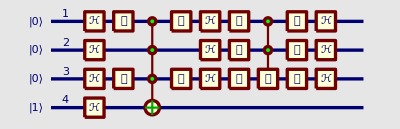
ℋ_{OverHat[1],OverHat[2],OverHat[3]}·𝒳_{OverHat[1],OverHat[2],OverHat[3]}·𝒞^{OverHat[1],OverHat[2]}[𝒵_OverHat[3]]·𝒳_{OverHat[1],OverHat[2],OverHat[3]}·ℋ_{OverHat[1],OverHat[2],OverHat[3]}·𝒳_{OverHat[1],OverHat[3]}·𝒞^{OverHat[1],OverHat[2],OverHat[3]}[𝒩𝒪𝒯_OverHat[4]]·𝒳_{OverHat[1],OverHat[3]}·ℋ_{OverHat[1],OverHat[2],OverHat[3],OverHat[4]}·|0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩
-Graphics-
-1/8 |0_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+1/8 |0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-1/8 |0_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+1/8 |0_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩-5/8 |0_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+5/8 |0_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-1/8 |0_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+1/8 |0_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩-1/8 |1_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+1/8 |1_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-1/8 |1_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+1/8 |1_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩-1/8 |1_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+1/8 |1_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-1/8 |1_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+1/8 |1_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩

```mathematica
n=3;
k=2;
mylist=Flatten[Position[IntegerDigits[k,2,n],0]];
circuitpart=Subscript[ℋ, n]·Subscript[𝒳, n]·(𝒞^(n-1))[Subscript[𝒵, n̂]]·Subscript[𝒳, n]·Subscript[ℋ, n]·Subscript[𝒳, mylist]·(𝒞^n)[Subscript[𝒩𝒪𝒯, OverHat[n+1]]]·Subscript[𝒳, mylist]·Subscript[ℋ, n+1]·(|Subscript[0, OverHat[1]]⟩)^(⊗n)·|Subscript[1, OverHat[n+1]]⟩;
Column[{
circuitpart,
QuantumPlot[circuitpart],
|h3⟩=QuantumEvaluate[circuitpart]}]
```

### Measurement gives with those kets that had their amplitude increased

The result of a measurement on the state |h3⟩ has a high probability of giving the state that meets the search criteria:

```mathematica
TraditionalForm[N[QuantumEvaluate[QubitMeasurement[|h3⟩,{OverHat[1],OverHat[2],OverHat[3]},FactorKet->False]]]]
```

Probability | Measurement | State
0.03125 | (0_1 | 0_2 | 0_3) | 0.707107 (|0001⟩-1. |0000⟩)
0.03125 | (0_1 | 0_2 | 1_3) | 0.707107 (|0011⟩-1. |0010⟩)
0.78125 | (0_1 | 1_2 | 0_3) | 0.707107 (|0101⟩-1. |0100⟩)
0.03125 | (0_1 | 1_2 | 1_3) | 0.707107 (|0111⟩-1. |0110⟩)
0.03125 | (1_1 | 0_2 | 0_3) | 0.707107 (|1001⟩-1. |1000⟩)
0.03125 | (1_1 | 0_2 | 1_3) | 0.707107 (|1011⟩-1. |1010⟩)
0.03125 | (1_1 | 1_2 | 0_3) | 0.707107 (|1101⟩-1. |1100⟩)
0.03125 | (1_1 | 1_2 | 1_3) | 0.707107 (|1111⟩-1. |1110⟩)
Probability | Measurement | State

The result of a measurement on the state |h3⟩ has a high probability of giving the state that meets the search criteria:

```mathematica
QuantumPlot3D[QuantumEvaluate[QubitMeasurement[|h3⟩,{OverHat[1],OverHat[2],OverHat[3]},FactorKet->False]]]
```

-Graphics3D--Graphics- | {0_1,0_2,0_3}
-Graphics- | {0_1,0_2,1_3}
-Graphics- | {0_1,1_2,0_3}
-Graphics- | {0_1,1_2,1_3}
-Graphics- | {1_1,0_2,0_3}
-Graphics- | {1_1,0_2,1_3}
-Graphics- | {1_1,1_2,0_3}
-Graphics- | {1_1,1_2,1_3}

### A second iteration gives the optimal increase of probability for three qubits

A second iteration further increments the amplitude of the kets that meets the criteria.
The optimal number of iterations is given by IntegerPart[π/(4 ArcSin(1/(√(2^n))))]. For three qubits, this optimal is two; further iterations would decrease (instead of increase) the desired amplitude. 
The state of the system is stored in |h4⟩

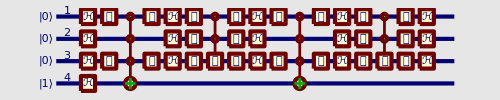
ℋ_{OverHat[1],OverHat[2],OverHat[3]}·𝒳_{OverHat[1],OverHat[2],OverHat[3]}·𝒞^{OverHat[1],OverHat[2]}[𝒵_OverHat[3]]·𝒳_{OverHat[1],OverHat[2],OverHat[3]}·ℋ_{OverHat[1],OverHat[2],OverHat[3]}·𝒳_{OverHat[1],OverHat[3]}·𝒞^{OverHat[1],OverHat[2],OverHat[3]}[𝒩𝒪𝒯_OverHat[4]]·𝒳_{OverHat[1],OverHat[3]}·ℋ_{OverHat[1],OverHat[2],OverHat[3]}·𝒳_{OverHat[1],OverHat[2],OverHat[3]}·𝒞^{OverHat[1],OverHat[2]}[𝒵_OverHat[3]]·𝒳_{OverHat[1],OverHat[2],OverHat[3]}·ℋ_{OverHat[1],OverHat[2],OverHat[3]}·𝒳_{OverHat[1],OverHat[3]}·𝒞^{OverHat[1],OverHat[2],OverHat[3]}[𝒩𝒪𝒯_OverHat[4]]·𝒳_{OverHat[1],OverHat[3]}·ℋ_{OverHat[1],OverHat[2],OverHat[3],OverHat[4]}·|0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩
-Graphics-
-1/16 |0_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+1/16 |0_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-1/16 |0_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+1/16 |0_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+11/16 |0_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-11/16 |0_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-1/16 |0_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+1/16 |0_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩-1/16 |1_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+1/16 |1_OverHat[1],0_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-1/16 |1_OverHat[1],0_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+1/16 |1_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩-1/16 |1_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+1/16 |1_OverHat[1],1_OverHat[2],0_OverHat[3],1_OverHat[4]⟩-1/16 |1_OverHat[1],1_OverHat[2],1_OverHat[3],0_OverHat[4]⟩+1/16 |1_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩

```mathematica
n=3;
k=2;
it=2;
mylist=Flatten[Position[IntegerDigits[k,2,n],0]];
circuitpart=Expand[(Subscript[ℋ, n]·Subscript[𝒳, n]·(𝒞^(n-1))[Subscript[𝒵, n̂]]·Subscript[𝒳, n]·Subscript[ℋ, n]·Subscript[𝒳, mylist]·(𝒞^n)[Subscript[𝒩𝒪𝒯, OverHat[n+1]]]·Subscript[𝒳, mylist])^it·Subscript[ℋ, n+1]·(|Subscript[0, OverHat[1]]⟩)^(⊗n)·|Subscript[1, OverHat[n+1]]⟩];
Column[{
circuitpart,
QuantumPlot[circuitpart,ImageSize->500],
|h4⟩=QuantumEvaluate[circuitpart]}]
```

### Measurement gives with those kets that had their amplitude increased

The result of a measurement on the state |h4⟩ has the highest probability of giving the state that meets the search criteria:

```mathematica
TraditionalForm[N[QuantumEvaluate[QubitMeasurement[|h4⟩,{OverHat[1],OverHat[2],OverHat[3]},FactorKet->False]]]]
```

Probability | Measurement | State
0.0078125 | (0_1 | 0_2 | 0_3) | 0.707107 (|0001⟩-1. |0000⟩)
0.0078125 | (0_1 | 0_2 | 1_3) | 0.707107 (|0011⟩-1. |0010⟩)
0.945313 | (0_1 | 1_2 | 0_3) | 0.707107 (|0100⟩-1. |0101⟩)
0.0078125 | (0_1 | 1_2 | 1_3) | 0.707107 (|0111⟩-1. |0110⟩)
0.0078125 | (1_1 | 0_2 | 0_3) | 0.707107 (|1001⟩-1. |1000⟩)
0.0078125 | (1_1 | 0_2 | 1_3) | 0.707107 (|1011⟩-1. |1010⟩)
0.0078125 | (1_1 | 1_2 | 0_3) | 0.707107 (|1101⟩-1. |1100⟩)
0.0078125 | (1_1 | 1_2 | 1_3) | 0.707107 (|1111⟩-1. |1110⟩)
Probability | Measurement | State

A Mathematica "Demonstration" implementing Grover's Algorithm can be found in this link:
Alexander Prokopenya, "Quantum Circuit Implementing Grover's Search Algorithm" from The Wolfram Demonstrations Project
http://demonstrations.wolfram.com/QuantumCircuitImplementingGroversSearchAlgorithm/

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx